```mathematica
x0=8.1;
y0=0.1;
z0=-0.1;
```

```mathematica
Ndata=5000;
```

```mathematica
poslist = Table[{x0,y0,z0},{i,1,Ndata}];
```

```mathematica
vx0=225;
vy0=10.0;
vz0=-10.0;
```

```mathematica
vellist=Table[{vx0,vy0,vz0},{i,1,Ndata}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetDirectory[NotebookDirectory[]];
pout=OpenWrite["pos1.test.dat"]
Write[pout,Ndata]
Export[pout,poslist];
Export["vel1.test.dat",vellist];
Close[pout]
```

OutputStream[pos1.test.dat,74]

pos1.test.dat

```mathematica
f1=OpenRead["newpos1.test.dat"];
Read[f1,Number]
Dimensions[newposlist=ReadList[f1,{Number,Number,Number}]]
Close[f1]
```

5000

{5000,3}

newpos1.test.dat

```mathematica
Mean[newposlist]
```

{8.1,0.100001,-0.100001}

```mathematica
posSun=Transpose[{newposlist[[All,1]]-8.0,newposlist[[All,2]],newposlist[[All,3]]}];
```

```mathematica
Dimensions[posSun]
```

{5000,3}

```mathematica
Dimensions[dSun=Sqrt[Total[Transpose[posSun^2]]]]
```

{5000}

```mathematica
1/Sqrt[3 0.1^2]
```

5.7735

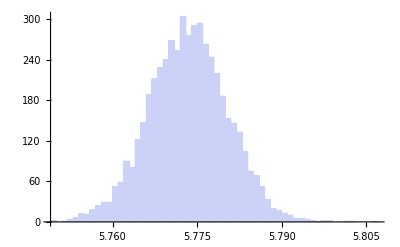

```mathematica
Histogram[1/dSun]
```

```mathematica
StandardDeviation[1/dSun]
```

0.00696558

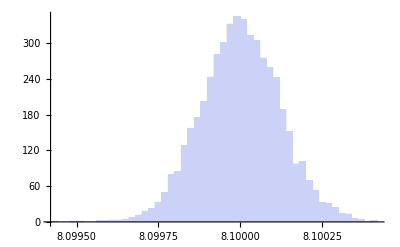

```mathematica
Histogram[newposlist[[All,1]]]
```

```mathematica
KolmogorovSmirnovTest[newposlist[[All,1]]]
```

0.740489

```mathematica
KolmogorovSmirnovTest[newposlist[[All,2]]]
```

0.740486

```mathematica
KolmogorovSmirnovTest[newposlist[[All,3]]]
```

0.740486

```mathematica
f1=OpenRead["newvel1.test.dat"];
Dimensions[newvellist=ReadList[f1,{Number,Number,Number}]]
Close[f1]
```

{5000,3}

newvel1.test.dat

```mathematica
Mean[newvellist]
```

{225.008,9.99275,-9.99582}

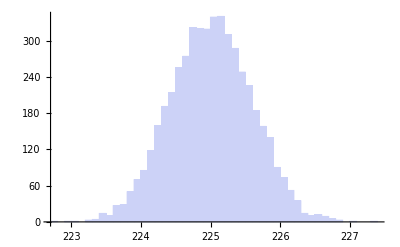

```mathematica
Histogram[newvellist[[All,1]]]
```

```mathematica
KolmogorovSmirnovTest[newvellist[[All,1]]]
```

0.898279

```mathematica
KolmogorovSmirnovTest[newvellist[[All,2]]]
```

0.765017

```mathematica
KolmogorovSmirnovTest[newvellist[[All,3]]]
```

0.503417

```mathematica
Dimensions[gdtest=ReadList["gasdevtest.out",Number]]
```

{5000}

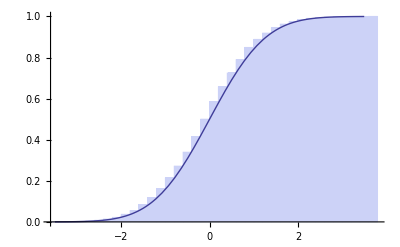

```mathematica
Show[Histogram[gdtest,Automatic,"CDF"],Plot[CDF[NormalDistribution[0,1],x],{x,-3.5,3.5}]]
```

```mathematica
Length[Commonest[gdtest]]
```

5000

```mathematica
KolmogorovSmirnovTest[gdtest,NormalDistribution[0,1],"TestConclusion",SignificanceLevel->0.001]
```

The null hypothesis that the data is distributed according to the NormalDistribution[0,1] is not rejected at the 0.1 percent level based on the Kolmogorov-Smirnov test.